```mathematica
(*第一大题第2问*)
```

```mathematica
F[n_]:=Module[{},
2*(4^n*(n!)^2/(2n)!)^2/(2*n+1)
]
```

```mathematica
N[F[50000],100]
N[Pi,100]
```

3.141576945822872670521234893861286884197515190165125147710687871965666678041753717118059267877655519

3.141592653589793238462643383279502884197169399375105820974944592307816406286208998628034825342117068

```mathematica
(*第一大题第3问*)
```

```mathematica
data0={{-1.9767,-0.108022},{1.0675,3.52312},{0.523336,1.91168},{1.44756,3.46338},{0.593401,2.12717},{-1.93801,0.138646},{-0.134274,0.839141},{1.45499,3.64625},{-1.93099,0.0705855},{-1.04388,-0.0918541},{-1.64074,0.0139767},{-1.60094,0.100703},{-1.66404,-0.0192112},{-0.668446,0.305261},{-0.187378,0.528536},{-0.116006,0.712391},{1.21922,3.40223},{-0.177995,0.725818},{-0.646504,0.14155},{0.367014,1.86582},{-0.715514,0.300889},{-0.58911,0.402169},{-1.07478,0.0591228},{-0.988166,0.0319816},{-1.41073,-0.0943066},{1.68028,3.17066},{0.776645,2.89104},{-0.203714,0.458002},{1.55742,3.47857},{1.97428,2.31653}}
```

{{-1.9767,-0.108022},{1.0675,3.52312},{0.523336,1.91168},{1.44756,3.46338},{0.593401,2.12717},{-1.93801,0.138646},{-0.134274,0.839141},{1.45499,3.64625},{-1.93099,0.0705855},{-1.04388,-0.0918541},{-1.64074,0.0139767},{-1.60094,0.100703},{-1.66404,-0.0192112},{-0.668446,0.305261},{-0.187378,0.528536},{-0.116006,0.712391},{1.21922,3.40223},{-0.177995,0.725818},{-0.646504,0.14155},{0.367014,1.86582},{-0.715514,0.300889},{-0.58911,0.402169},{-1.07478,0.0591228},{-0.988166,0.0319816},{-1.41073,-0.0943066},{1.68028,3.17066},{0.776645,2.89104},{-0.203714,0.458002},{1.55742,3.47857},{1.97428,2.31653}}

```mathematica
slu=Fit[data0,{1,x,x^2,x^3,x^4,x^5,x^6,x^7,x^8},x]
```

0.883464+1.57292 x+1.46116 x^2+0.334275 x^3-0.917564 x^4-0.327192 x^5+0.259277 x^6+0.045436 x^7-0.0296934 x^8

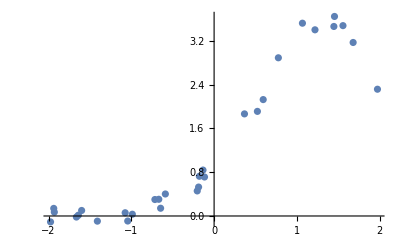

```mathematica
G0=ListPlot[data0]
```

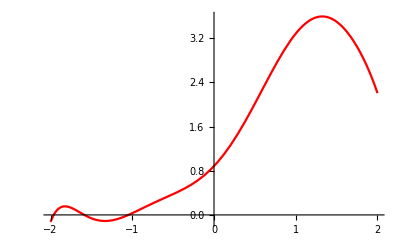

```mathematica
G1=Plot[slu,{x,-2,2},PlotStyle->Red]
```

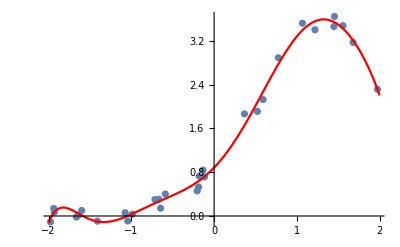

```mathematica
Show[G0,G1]
```

```mathematica
SJ=Transpose[data0][[2]]
```

{-0.108022,3.52312,1.91168,3.46338,2.12717,0.138646,0.839141,3.64625,0.0705855,-0.0918541,0.0139767,0.100703,-0.0192112,0.305261,0.528536,0.712391,3.40223,0.725818,0.14155,1.86582,0.300889,0.402169,0.0591228,0.0319816,-0.0943066,3.17066,2.89104,0.458002,3.47857,2.31653}

```mathematica
YC=Table[slu/.{x-> data0[[i,1]]},{i,1,Length[SJ]}]
```

{-0.0447251,3.39455,2.0787,3.54576,2.27539,0.0540946,0.697514,3.53994,0.0677087,0.00177313,0.0450214,0.0114214,0.064916,0.264802,0.636792,0.719979,3.55866,0.647046,0.279497,1.65593,0.232881,0.317586,-0.0178465,0.0393918,-0.0994047,3.20766,2.77742,0.619402,3.42571,2.31426}

```mathematica
Mean[SJ]
Mean[YC]
```

1.21039

1.21039

```mathematica
Correlation[SJ,YC]
```

0.997218

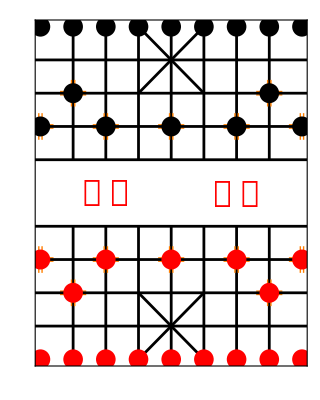

```mathematica
(*第二大题第1问*)
shizi[{x_,y_},size_]:=Graphics[{Thick,Orange,Line[{{{x-size,y-0.05},{x-0.05,y-0.05},{x-0.05,y-size}},{{x+size,y-0.05},{x+0.05,y-0.05},{x+0.05,y-size}},{{x-size,y+0.05},{x-0.05,y+0.05},{x-0.05,y+size}},{{x+size,y+0.05},{x+0.05,y+0.05},{x+0.05,y+size}}}]}]
shiziN={Table[shizi[{i,2},0.4],{i,{1,7}}],Table[shizi[{i,8},0.4],{i,{1,7}}],Table[shizi[{i,3},0.4],{i,{0,2,4,6,8}}],Table[shizi[{i,7},0.4],{i,{0,2,4,6,8}}]};
xiangqi={Table[Graphics[{Thick,Red,Disk[{i,2},0.3]}],{i,{1,7}}],
Table[Graphics[{Thick,Black,Disk[{i,8},0.3]}],{i,{1,7}}],
Table[Graphics[{Thick,Red,Disk[{i,3},0.3]}],{i,{0,2,4,6,8}}],
Table[Graphics[{Thick,Black,Disk[{i,7},0.3]}],{i,{0,2,4,6,8}}],
Table[Graphics[{Thick,Red,Disk[{i,0},0.3]}],{i,0,8}],
Table[Graphics[{Thick,Black,Disk[{i,10},0.3]}],{i,0,8}]};
Show[Graphics[{Black,Thickness[0.005],Line[Table[{{i,0},{i,4}},{i,7}]],Line[Table[{{i,10},{i,6}},{i,7}]],Line[{{{3,0},{5,2}},{{5,0},{3,2}},{{3,8},{5,10}},{{5,8},{3,10}}}],Text[Style["楚 河",30,Red],{2,5}],Text[Style["汉 界",30,Red],{6,5},Automatic,{-1,0}]},Frame->True,FrameStyle->Directive[Brown,Thickness[0.01]],GridLines->{None,Delete[Range[9],5]},GridLinesStyle->Directive[Black,Thickness[0.005]],PlotRange->{{0,8},{0,10}},AxesOrigin->{0,0},FrameTicks->None],crossN,xiangqi]
```

```mathematica
(*第二题第2问*)
```

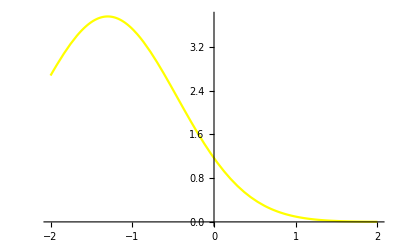

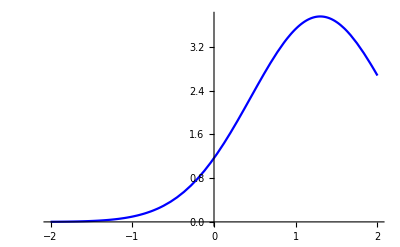

```mathematica
P0=Plot[8*Table[PDF[NormalDistribution[μ,0.85],x],{μ,{-1.3}}]//Evaluate,{x,-2,2},PlotStyle->Yellow]
P1=Plot[8*Table[PDF[NormalDistribution[μ,0.85],x],{μ,{1.3}}]//Evaluate,{x,-2,2},PlotStyle->Blue]
```

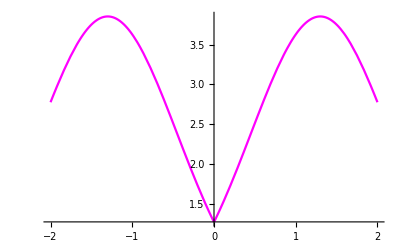

```mathematica
f[x_]:=If[x≥0,8*Table[PDF[NormalDistribution[μ,0.85],x],{μ,{1.3}}]+0.1//Evaluate,8*Table[PDF[NormalDistribution[μ,0.85],x],{μ,{-1.3}}]+0.1//Evaluate]
P3=Plot[f[x],{x,-2,2},PlotStyle->Magenta]
```

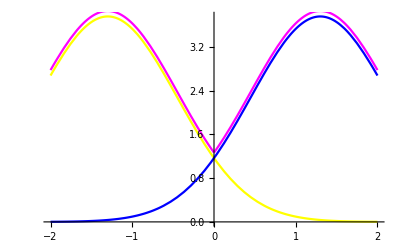

```mathematica
Show[P0,P1,P3]
```

```mathematica
(*第三题选作第2题*)
```

```mathematica
RandomWalk[x_,n_]:=Module[{xrand,yrand,k,pointlist,list,i},
xrand=0;
yrand=0;
list=RealDigits[N[x,n]][[1]];
pointlist={{0,0}};
For[i=1,i≤n,i++,k=list[[i]];
xrand=xrand+Sin[2*k*Pi/10] ;
yrand=yrand+Cos[2*k*Pi/10] ;

pointlist=AppendTo[pointlist,{xrand,yrand}]];
Graphics[{Black,Line[pointlist]}]]
```

```mathematica
list=RealDigits[N[234769516/999999999,50000]][[1]]
```

{2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,49676,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,6,9,5,1,6,2,3,4,7,7}
 |  |  |  |

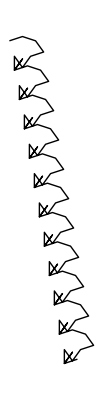

```mathematica
RandomWalk[234769516/999999999,100]
```

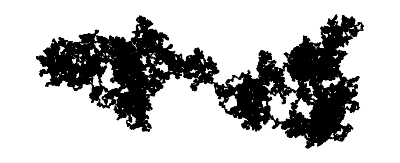

```mathematica
RandomWalk[Sqrt[2],50000]
```

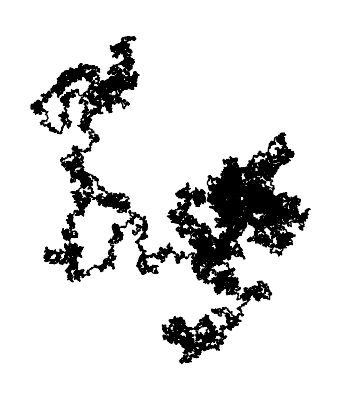

```mathematica
RandomWalk[E,50000]
```

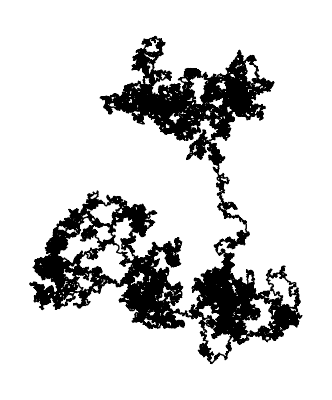

```mathematica
RandomWalk[Log10[2],50000]
```